# Remainders Analysis

```mathematica
(*Preliminaries*)
SetDirectory[FileNameJoin[{NotebookDirectory[],"Data", "PeriodFitData"}] ];

(*Period formula*)
truePeriod [slope_, periodGuess_]:=periodGuess/(1-slope);
σtruePeriod[slopes_, periodGuess_,σslopes_]:= 1/(1/periodGuess-slopes)^2*σslopes;
```

## First Crab Observation --------------------------

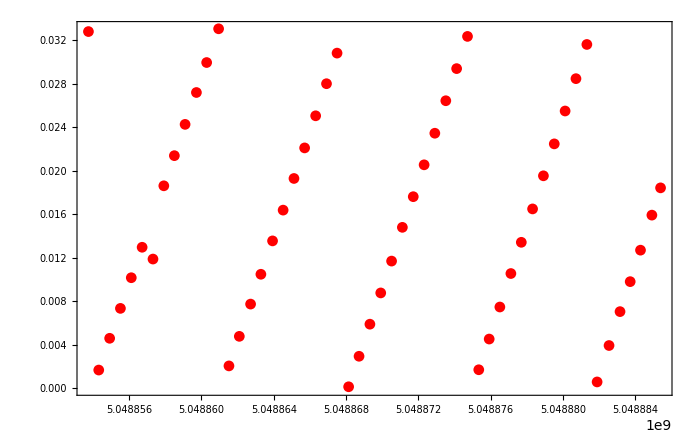

```mathematica
(*Estimated Period*)
periodGuess = 0.0337552412;

(*Import Data*)
times = ReadList["crab1times.txt", Number];
remainders= ReadList["crab1remainders.txt", Number];

data = Transpose[{times, remainders}];
ListPlot[data, PlotRange->All, Frame->True, ImageSize->700, PlotStyle->{Red, Thick}]
```

{4.75168×10^-6,4.81236×10^-6,4.89931×10^-6,4.99468×10^-6,5.07063×10^-6}

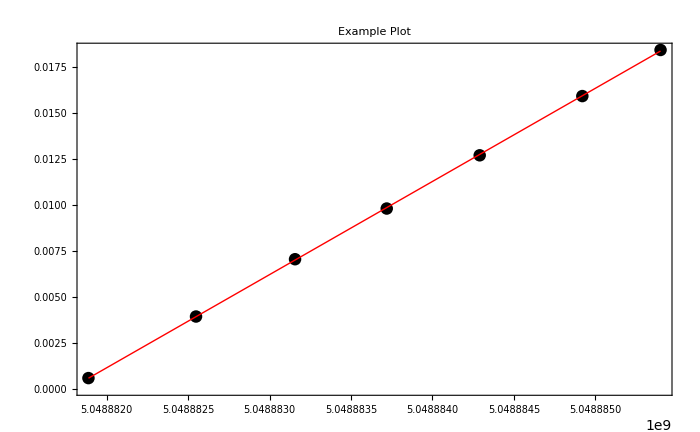

χ^2 values: {0.00001444,1.3946×10^-8,2.3245×10^-8,1.6302×10^-8,1.0415×10^-8}

Reduced χ^2 values: {1.444×10^-6,1.5495×10^-9,2.3245×10^-9,1.8114×10^-9,2.0831×10^-9}

The probability of getting this χ^2: P = {1.,1.,1.,1.,1.}

```mathematica
(*Separate data into full periods*)
peaksIdxs = FindPeaks[remainders][[All,1]];
sepData =Table[data[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,1,Length@peaksIdxs - 1}];

(*For each period, find slopes, errors and the residuals*)
slopes = Table[LinearModelFit[sepData[[i]],x,x]["BestFitParameters"][[2]], {i,1,Length@sepData}]
σslopes = Table[LinearModelFit[sepData[[i]],x,x]["ParameterErrors"][[2]], {i,1,Length@sepData}];
residuals = Table[LinearModelFit[sepData[[i]],x,x]["FitResiduals"], {i,1,Length@sepData}];

(*Fit statistics*)
nDof = Table[Length@sepData[[i]]-2,{i,1, Length@sepData}];
χsq = ParallelTable[Total[(residuals[[i]])^2],{i,1,Length@residuals}];
p=ParallelTable[Integrate[(E^(-χs/2)*χs^(nDof[[i]]/2-1))/(2^(nDof[[i]]/2)*Gamma[nDof[[i]]/2]),{χs,χsq[[i]],Infinity}],{i,1, Length@χsq}];
(*Test plot*)
lm = LinearModelFit[sepData[[5]],x,x];
xdata = sepData[[5]][[All,1]];
Show[ListPlot[sepData[[5]],PlotStyle->Black], Plot[lm[x],{x, Min[xdata], Max[xdata]}, PlotRange->All, PlotStyle->{Red, Thick}], Frame->True, ImageSize->700, PlotLabel->"Example Plot", LabelStyle->Directive[20], FrameTicksStyle->{Directive[20],Directive[12]}]

(*Outputting the results*)

Text[Row[{Style["χ^2 values:", Bold]," ", NumberForm[χsq,5]}]] 
Text[Row[{Style["Reduced χ^2 values:", Bold]," ", NumberForm[χsq/nDof,5]}]]  
Text[Row[{Style["The probability of getting this χ^2:", Bold]," P = ",p}]]
```

```mathematica
(*Get rid of bad slopes*)
newSlopes = Delete[slopes,1];
newσSlopes = Delete[σslopes,1];

(*Calculate the periods*)
periods = Table[truePeriod[slopes[[i]],periodGuess],{i,1,Length@slopes}]
σperiods = σtruePeriod[slopes, periodGuess,σslopes]

(*Compute weighted data*)
wdata = WeightedData[periods, σperiods];
meanPeriod1 = Mean[wdata];
σmeanPeriod1 = StandardDeviation[wdata];
Export["crab1period.txt", {meanPeriod1,σmeanPeriod1}];

(*Display Results*)
Text[Row[{Style["Mean Period:", Bold]," ", NumberForm[meanPeriod1,20]}]]
Text[Row[{Style["Error on Mean Period:", Bold]," ", NumberForm[σmeanPeriod1,20]}]]
```

{0.0337554,0.0337554,0.0337554,0.0337554,0.0337554}

{1.90919×10^-10,7.12503×10^-12,7.66998×10^-12,7.71123×10^-12,1.67657×10^-11}

Mean Period: 0.03375540288333157

Error on Mean Period: 5.737285390827286×10^-9

## Fitting one straight line

{5.04886×10^9,5.04886×10^9,5.04886×10^9,5.04886×10^9,5.04886×10^9,5.04886×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04887×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04888×10^9,5.04889×10^9}

{0.00204062,0.00475919,0.00772573,0.0104686,0.0135384,0.0163677,0.0192796,0.0220901,0.0250431,0.0279944,0.0308084,0.0338771,0.0366824,0.0396326,0.0425074,0.0454365,0.0485396,0.0513589,0.0542899,0.057195,0.0601834,0.0631384,0.0660996,0.0691972,0.0720215,0.0749676,0.0780473,0.0809188,0.0839892,0.0870346,0.0899712,0.0929946,0.0959694,0.0991151,0.101832,0.105182,0.108299,0.111056,0.113951,0.117173,0.119681}

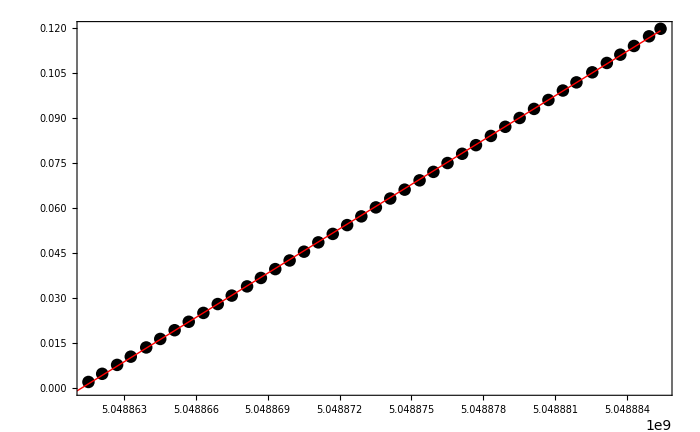

Period: 0.03375540747532719

Error on Mean Period: 1234

```mathematica
(*Aligning the lines*)
sepRemainders =Table[remainders[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,1,Length@peaksIdxs - 1}];
newTimes = Flatten[Table[times[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,2,Length@peaksIdxs - 1}]]
newRemainders = Flatten[Table[sepRemainders[[i]]+(i-2)*periodGuess,{i,2,Length@sepRemainders}]]
newData = Transpose[{newTimes, newRemainders}];

(*Fittng data*)
lm = LinearModelFit[newData,x,x];
Show[ListPlot[newData, PlotStyle->{Black}], Plot[lm[x],{x,Min[times],Max[times]},PlotStyle->{Red, Thick}] ,Frame->True, ImageSize->700]
slope = lm["BestFitParameters"][[2]];
thisPeriod = truePeriod[slope,periodGuess];

(*Display Results*)
Text[Row[{Style["Period:", Bold]," ", NumberForm[thisPeriod,20]}]]
Text[Row[{Style["Error on Mean Period:", Bold]," ", NumberForm[1234,20]}]]
```

## Second Crab Observation ------------------------------

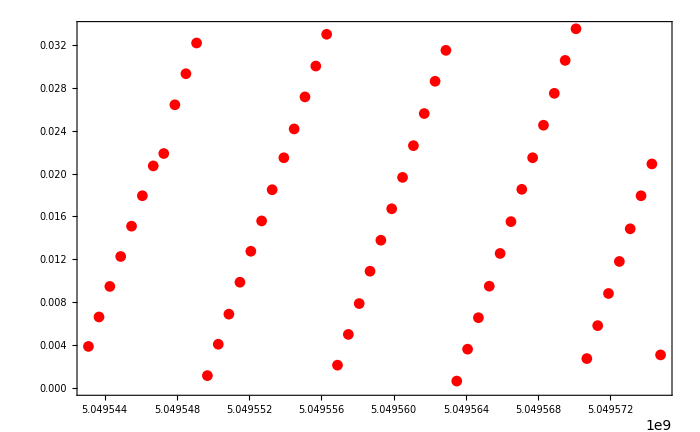

```mathematica
(*Estimated period*)
periodGuess = 0.0337555307;
(*Import Data*)
times = ReadList["crab2times.txt", Number];
remainders= ReadList["crab2remainders.txt", Number];

data = Transpose[{times, remainders}];
ListPlot[data, PlotRange->All, Frame->True, ImageSize->700, PlotStyle->{Red, Thick}]
```

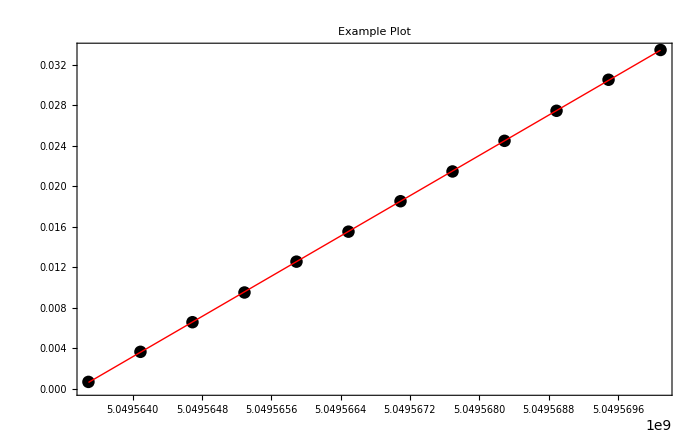

χ^2 values: {2.436×10^-6,2.6042×10^-8,2.6232×10^-8,1.6651×10^-8,4.6602×10^-9}

Reduced χ^2 values: {2.7066×10^-7,2.6042×10^-9,2.9146×10^-9,1.6651×10^-9,9.3203×10^-10}

The probability of getting this χ^2: P = {1.,1.,1.,1.,1.}

```mathematica
(*Separate data into full periods*)
peaksIdxs = FindPeaks[remainders][[All,1]];
PrependTo[peaksIdxs,0];
sepData =Table[data[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,1,Length@peaksIdxs - 1}];

(*For each period, find slopes, errors and the residuals*)
slopes = Table[LinearModelFit[sepData[[i]],x,x]["BestFitParameters"][[2]], {i,1,Length@sepData}];
σslopes = Table[LinearModelFit[sepData[[i]],x,x]["ParameterErrors"][[2]], {i,1,Length@sepData}];
residuals = Table[LinearModelFit[sepData[[i]],x,x]["FitResiduals"], {i,1,Length@sepData}];

(*Fit statistics*)
nDof = Table[Length@sepData[[i]]-2,{i,1, Length@sepData}];
χsq = ParallelTable[Total[(residuals[[i]])^2],{i,1,Length@residuals}];
p=ParallelTable[Integrate[(E^(-χs/2)*χs^(nDof[[i]]/2-1))/(2^(nDof[[i]]/2)*Gamma[nDof[[i]]/2]),{χs,χsq[[i]],Infinity}],{i,1, Length@χsq}];
(*Test plot*)
lm = LinearModelFit[sepData[[4]],x,x];
xdata = sepData[[4]][[All,1]];
Show[ListPlot[sepData[[4]],PlotStyle->Black], Plot[lm[x],{x, Min[xdata], Max[xdata]}, PlotRange->All, PlotStyle->{Red, Thick}], Frame->True, ImageSize->700, PlotLabel->"Example Plot", LabelStyle->Directive[20], FrameTicksStyle->{Directive[20],Directive[12]}]

(*Outputting the results*)

Text[Row[{Style["χ^2 values:", Bold]," ", NumberForm[χsq,5]}]] 
Text[Row[{Style["Reduced χ^2 values:", Bold]," ", NumberForm[χsq/nDof,5]}]]  
Text[Row[{Style["The probability of getting this χ^2:", Bold]," P = ",p}]]
```

```mathematica
(*Get rid of bad slopes*)
newSlopes = Delete[slopes,2];
newσSlopes = Delete[σslopes,2];

(*Calculate the periods*)
periods = truePeriod[slopes, periodGuess];
σperiods = σtruePeriod[slopes,periodGuess,σslopes];

(*Compute weighted data*)
wdata = WeightedData[periods, σperiods];
meanPeriod2 = Mean[wdata];
σmeanPeriod2 = StandardDeviation[wdata];
Export["crab2period.txt", {meanPeriod2,σmeanPeriod2}];

(*Display Results*)
Text[Row[{Style["Mean Period:", Bold]," ", NumberForm[meanPeriod2,20]}]]
Text[Row[{Style["Error on Mean Period:", Bold]," ", NumberForm[σmeanPeriod2,20]}]]
```

Mean Period: 0.03375569072289549

Error on Mean Period: 6.473524733397306×10^-9

## Fitting one straight line

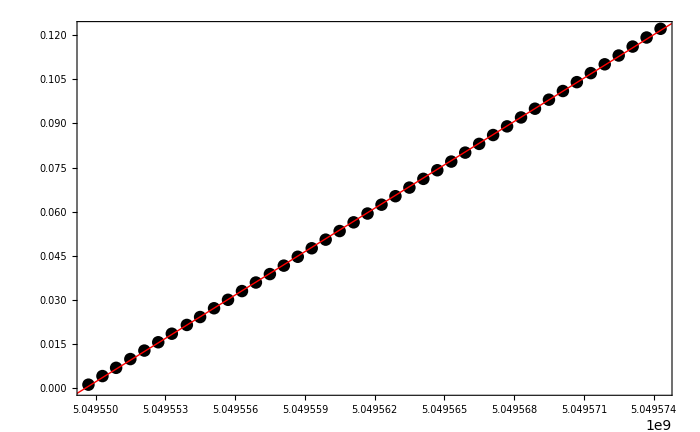

Period: 0.03375569668845487

Error on Mean Period: 1234

```mathematica
(*Aligning the lines*)
sepRemainders =Table[remainders[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,1,Length@peaksIdxs - 1}];
newTimes = Flatten[Table[times[[peaksIdxs[[i]]+1;; peaksIdxs[[i+1]]]],{i,2,Length@peaksIdxs - 1}]];
newRemainders = Flatten[Table[sepRemainders[[i]]+(i-2)*periodGuess,{i,2,Length@sepRemainders}]];
newData = Transpose[{newTimes, newRemainders}];

(*Fittng data*)
lm = LinearModelFit[newData,x,x];
Show[ListPlot[newData, PlotStyle->{Black}], Plot[lm[x],{x,Min[times],Max[times]},PlotStyle->{Red, Thick}] ,Frame->True, ImageSize->700]
slope = lm["BestFitParameters"][[2]];
thisPeriod = truePeriod[slope,periodGuess];

(*Display Results*)
Text[Row[{Style["Period:", Bold]," ", NumberForm[thisPeriod,20]}]]
Text[Row[{Style["Error on Mean Period:", Bold]," ", NumberForm[1234,20]}]]
```

## Derivative and Quantities of Interest -------------------------------------------

```mathematica
(*Constants*)
c = 299792458;

(*Fromulas*)
age[p_,pder_]:=p/(2*pder*86400*365.25);
B[I_,R_,α_,p_,pder_]:=√((3*c^3*I)/(8*π^2*R^6*(Sin[α])^2)*p*pder)
```

```mathematica
(*Frequency Derivative*)
δt = (58443.968055545330040-58435.969024813132347)*86400;
δp = meanPeriod2-meanPeriod1;
pder = δp/δt;

(*Age*)
a = age[meanPeriod2, pder];
Text[Row[{Style["Age of pulsar:", Bold]," ", NumberForm[a,20]}]]

(*Magnetic Field*)
```

Age of pulsar: 1284.143790801936